```mathematica
alcst = AlcubierreSpacetime[];
minst = MinkowskiSpacetime[];
```

```mathematica
sol = TraceNullGeodesic[
minst,
{0,0,0,0}, {1,1,0,0}
];
```

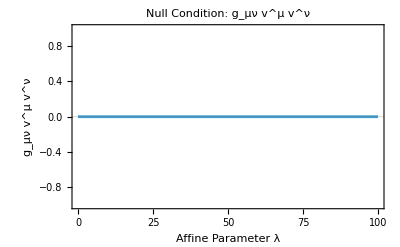

```mathematica
VerifyNullCondition[minst, sol]
```